## Introduction

Special case J = K -- can we predict anything here?

1. S_±(K)  in the double phase wave state?
2. S_±(K) in the sync state?

Can I predict a boundary when E>0?

## E = 0

### Find fixed points

I assume below that ϕ_+=ϕ_-=0.

```mathematica
es={
2 Cos[η]Sin[2 ξ-α]-k sp Sin[ξ],
2 Sin[η]Cos[2 ξ-α]-k sm Sin[η]
};

assum={0≤α≤2π,0≤sm≤1,0≤sp≤1,k∈Reals};
fp=Solve[es=={0,0},{ξ,η}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
Length[fp]
```

48

There are 48, but really only two types. The first type is

```mathematica
Simplify[fp[[1;;10]]]
```

{{ξ→-ArcCos[-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2)))],η→-ArcCos[(k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]},{ξ→-ArcCos[-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2)))],η→ArcCos[(k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]},{ξ→ArcCos[-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2)))],η→-ArcCos[(k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]},{ξ→ArcCos[-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2)))],η→ArcCos[(k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]},{ξ→-ArcCos[1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2)))],η→-ArcCos[(k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]},{ξ→-ArcCos[1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2)))],η→ArcCos[(k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]},{ξ→ArcCos[1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2)))],η→-ArcCos[(k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]},{ξ→ArcCos[1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2)))],η→ArcCos[(k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]},{ξ→-ArcCos[-1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2)))],η→-ArcCos[-(k sp √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) (-4+k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]},{ξ→-ArcCos[-1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2)))],η→ArcCos[-(k sp √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) (-4+k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]}}

```mathematica
TableForm[fp[[32;;38]]]
```

ξ→ArcCos[√((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))))))] | η→ArcCos[(Csc[α]^2 Sec[α] √((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))))) (k^6 sp^6-4 k^4 sp^4 Sin[α]^2+192 k^2 sp^2 Cos[α]^2 Sin[α]^2-64 k^2 sp^2 Sin[α]^4+256 Cos[α]^2 Sin[α]^4+256 Sin[α]^6-k^6 sp^6 ((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))))))-32 k^4 sp^4 Cos[α]^2 ((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))))))+32 k^4 sp^4 Sin[α]^2 ((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))))))-256 k^2 sp^2 Cos[α]^2 Sin[α]^2 ((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))))))-1024 Cos[α]^4 Sin[α]^2 ((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))))))-2048 Cos[α]^2 Sin[α]^4 ((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))))))-1024 Sin[α]^6 ((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))))))+32 k^4 sp^4 Cos[α]^2 (((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))))))^2+256 k^2 sp^2 Cos[α]^4 (((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))))))^2-32 k^4 sp^4 Sin[α]^2 (((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))))))^2+512 k^2 sp^2 Cos[α]^2 Sin[α]^2 (((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))))))^2+1024 Cos[α]^4 Sin[α]^2 (((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))))))^2+256 k^2 sp^2 Sin[α]^4 (((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))))))^2+2048 Cos[α]^2 Sin[α]^4 (((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))))))^2+1024 Sin[α]^6 (((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))))))^2-256 k^2 sp^2 Cos[α]^4 (((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))+1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(128 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))-(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))-((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3))-(-(-k^4 sp^4-16 k^2 sp^2 Cos[α]^2+20 k^2 sp^2 Sin[α]^2-64 Cos[α]^2 Sin[α]^2-64 Sin[α]^4)/(16 (Cos[α]^2+Sin[α]^2)^2)-((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^3)/(512 (Cos[α]^2+Sin[α]^2)^6)+((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4) (k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4))/(512 (Cos[α]^2+Sin[α]^2)^4))/(4 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))/(768 2^(1/3)))))))^3-512 k^2 sp^2 Cos[α]^2 Sin[α]^2 (((k^2 sp^2 Cos[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+Cos[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-(k^2 sp^2 Sin[α]^2)/(32 (Cos[α]^2+Sin[α]^2)^2)+(Cos[α]^2 Sin[α]^2)/((Cos[α]^2+Sin[α]^2)^2)+Sin[α]^4/(2 (Cos[α]^2+Sin[α]^2)^2)-1/2 √(((-k^2 sp^2 Cos[α]^2-16 Cos[α]^4+k^2 sp^2 Sin[α]^2-32 Cos[α]^2 Sin[α]^2-16 Sin[α]^4)^2)/(256 (Cos[α]^2+Sin[α]^2)^4)-(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(256 (Cos[α]^2+Sin[α]^2)^2)+(k^4 sp^4+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4)/(768 (Cos[α]^4+2 Cos[α]^2 Sin[α]^2+Sin[α]^4))+(24576-7168 k^2 sp^2+960 k^4 sp^4+k^8 sp^8+32768 Cos[2 α]-8192 k^2 sp^2 Cos[2 α]+256 k^4 sp^4 Cos[2 α]-64 k^6 sp^6 Cos[2 α]+8192 Cos[4 α]-1024 k^2 sp^2 Cos[4 α]+320 k^4 sp^4 Cos[4 α])/(384 2^(2/3) (2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968 k^8 sp^8 Cos[α]^8 Sin[α]^8+133590662774784 k^6 sp^6 Cos[α]^10 Sin[α]^8-356241767399424 k^4 sp^4 Cos[α]^12 Sin[α]^8+347892350976 k^10 sp^10 Cos[α]^4 Sin[α]^10-11132555231232 k^8 sp^8 Cos[α]^6 Sin[α]^10+111325552312320 k^6 sp^6 Cos[α]^8 Sin[α]^10-356241767399424 k^4 sp^4 Cos[α]^10 Sin[α]^10-1855425871872 k^8 sp^8 Cos[α]^4 Sin[α]^12+29686813949952 k^6 sp^6 Cos[α]^6 Sin[α]^12-118747255799808 k^4 sp^4 Cos[α]^8 Sin[α]^12))^(1/3))+((2 k^12 sp^12-192 k^10 sp^10 Cos[α]^2+7680 k^8 sp^8 Cos[α]^4-163840 k^6 sp^6 Cos[α]^6+1966080 k^4 sp^4 Cos[α]^8-12582912 k^2 sp^2 Cos[α]^10+33554432 Cos[α]^12+192 k^10 sp^10 Sin[α]^2-6144 k^8 sp^8 Cos[α]^2 Sin[α]^2-24576 k^6 sp^6 Cos[α]^4 Sin[α]^2+2752512 k^4 sp^4 Cos[α]^6 Sin[α]^2-31457280 k^2 sp^2 Cos[α]^8 Sin[α]^2+100663296 Cos[α]^10 Sin[α]^2+6144 k^8 sp^8 Sin[α]^4-24576 k^6 sp^6 Cos[α]^2 Sin[α]^4+1769472 k^4 sp^4 Cos[α]^4 Sin[α]^4-25165824 k^2 sp^2 Cos[α]^6 Sin[α]^4+100663296 Cos[α]^8 Sin[α]^4+65536 k^6 sp^6 Sin[α]^6-786432 k^4 sp^4 Cos[α]^2 Sin[α]^6-6291456 k^2 sp^2 Cos[α]^4 Sin[α]^6+33554432 Cos[α]^6 Sin[α]^6+√(452984832 k^14 sp^14 Cos[α]^4 Sin[α]^6-28991029248 k^12 sp^12 Cos[α]^6 Sin[α]^6+724775731200 k^10 sp^10 Cos[α]^8 Sin[α]^6-8813272891392 k^8 sp^8 Cos[α]^10 Sin[α]^6+51951924412416 k^6 sp^6 Cos[α]^12 Sin[α]^6-118747255799808 k^4 sp^4 Cos[α]^14 Sin[α]^6+27179089920 k^12 sp^12 Cos[α]^4 Sin[α]^8+260919263232 k^10 sp^10 Cos[α]^6 Sin[α]^8-14959371091968

Hard to read, but ultimately the roots of an polynomial of degree 8. These are complicated,but maybe I can do use perturbation theory to use it. Can you find the fixed points for E > 0 too?

### Plot

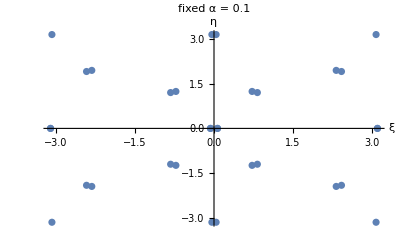

```mathematica
sub1={sp->0.99,sm->0.05,k->1,α->0.1};
ListPlot[{ξ,η}/.fp/.sub1,AxesLabel->{"ξ","η"},LabelStyle->15,PlotLabel->"fixed α = 0.1"]//Quiet
```

So there’s a family of fixed points. If I plot for different α, I should see the 

1. static phase wave
2. double phase wave
3. sync states

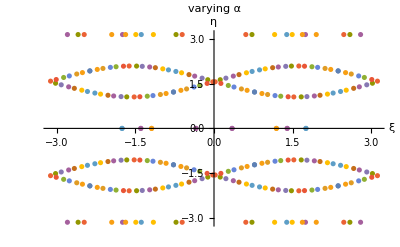

```mathematica
sub1={sp->0.99,sm->0.05,k->1};
data=Table[{ξ,η}/.fp/.sub1/.α->a1,{a1,0,2π,0.5}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15,PlotLabel->"varying α"]
```

Replot for finder α

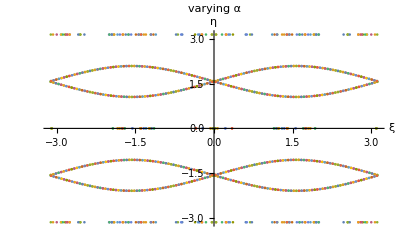

```mathematica
sub1={sp->0.99,sm->0.05,k->1};
data=Table[{ξ,η}/.fp/.sub1/.α->a1,{a1,0,2π,0.1}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15,PlotLabel->"varying α"]
```

1. The static phase wave and double phase waves are clear. Those are the straight lines
2. I’m guessing the loops are (1) the sync state (one lobe stable, the other lobes unstable). (2) the traveling loops?
Plot a single fixed point for varying α. Now do it for each fixed point.

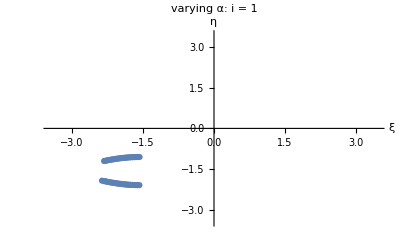
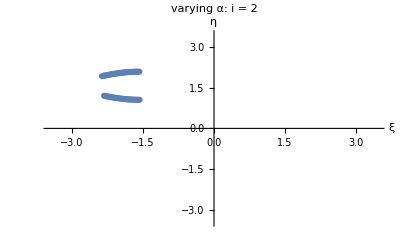
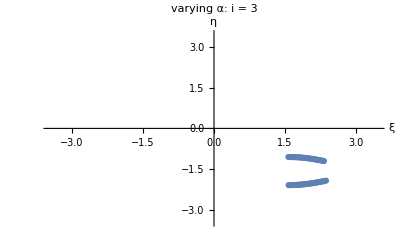
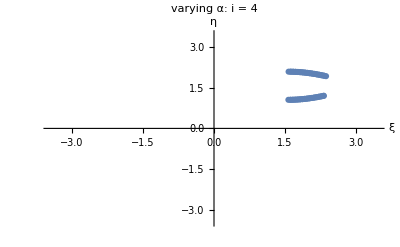
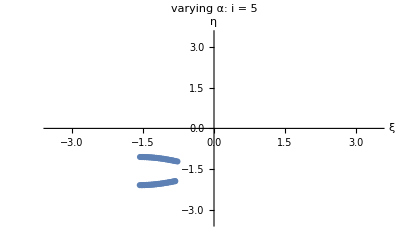
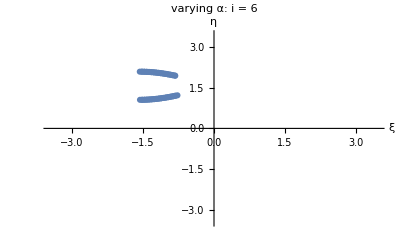
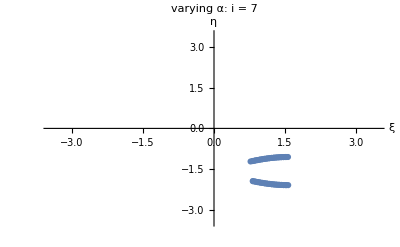
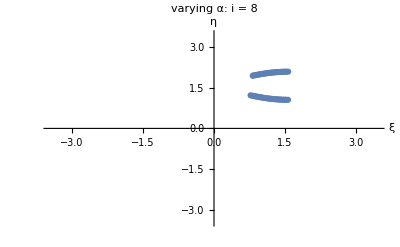

```mathematica
Table[
sub1={sp->0.99,sm->0.05,k->1};
data=Table[{ξ,η}/.fp[[i]]/.sub1/.α->a1,{a1,0,2π,0.1}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15,PlotRange->{{-1.1π,1.1π},{-1.1π,1.1π}},PlotLabel->"varying α: i = "<>ToString[i]]//Quiet,
{i,1,Length[fp]}
]
```

Yes, the first few are the sync state. Good.

## Find S_+ using perturbation theory when E = 0

We know S_+= ∫ cos ξ(α,S_+,S_-) d α and S_-=∫ cos η(α, S_+,S_-) d α where I have assumed wlog that ϕ_±=0 (?). So we have a pair of self-consistent equations. The are complicated, of course, since the fixed points are complex, but in theory we have them. I wonder if I expand in a perturbation series:

S_+= a_0 + a_1 k+a_2 k^2+...
S_-=b_0 + b_1 k+b_2 k^2+ ...

Can I derive 

1. S_± is the sync and double phase wave states?
2. We have k

### Simulations for N >> 1

#### Animation

```mathematica
(*Preamble*)
{dt,n,T}={0.5,100,400}; 
{J,k,b,e}={1,-0.5,1,0};
{Ex,Eθ} = {e,e};
{b1,b2} = {b,b};

{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

{z0,pin,znew}={Table[RandomReal[{0π,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;

results={};
Dynamic[results] (*For dynamic plotting*)
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)

(*Main sim*)
{Wp,Wm}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;
{Wp1,Wm1}=findWs[znew];
AppendTo[Wp,Abs[Wp1]];AppendTo[Wm,Abs[Wm1]];
results=plotResults[znew,pin]
]

ListPlot[{Abs[Wp],Abs[Wm]}]
```

#### S(K) -- freeze J = b = 1

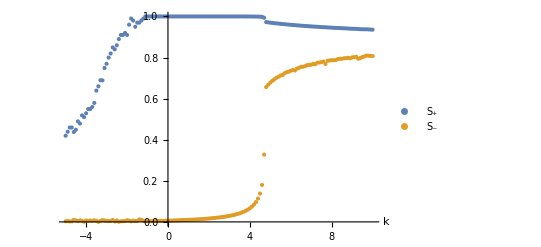

```mathematica
(*Start from incoherence: z_new = uniform on [0,2π]*)
data1=ParallelTable[
{dt,n,T}={0.25,200,300};
{J,b}={1,1};
{Ex,Eθ} = {0,0};
{b1,b2} = {b,b};
{z0,pin,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],Table[RandomReal[{0,2π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]}; (*z = [x,θ]*)
pin=Table[Table[2 Pi i / (n-1),{i,0,n-1}]//N,{j,1,2}];
z00 = z0;
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{Wps,Wms}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,Ex,Eθ,pin,b1,b2];
z0=znew;t++;{Wp,Wm}=findWs[znew];
AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75Length[Wps]];
{Sp,Sm}={Wps[[cutoff;;-1]]//Abs//Mean,Wms[[cutoff;;-1]]//Abs//Mean};
If[Sp<Sm,{Sp,Sm}={Sm,Sp}];
{k,Sp,Sm},
{k,-5,10,0.1}
];

ListPlot[{data1[[All,{1,2}]],data1[[All,{1,3}]]},AxesLabel->{Style["k",15,Italic]},LabelStyle->15,PlotLegends->{"S_+","S_-"},PlotLabel->""]
```

1. You can see the three states here: double phase wave --> static phase wave --> sync 
2. Or maybe I should plot S(b) and expand in powers of b? 
3. Is it a first order phase transtions?

#### Focus on S_±(K) in sync state

This should be a good warm up. First lets find the K_c. We previously derived:

```mathematica
Clear[b,k]
Solve[-8 b-j-k-√(j^2+34 j k+k^2)==0,k]/.b->1/.j->1
```

{{k→5}}

Then the form of the perturbation series is:

S_+=1 + a_1(k-k_c)+(a_2(k-k_c))^2+...
S_-=b_0 + b_1(k-k_c)+(b_2(k-k_c))^2+...

where k_c=5. Note I have guessed a_0=1.

```mathematica
Clear[b1,b2];
series={
sp->1+a1 ϵ+a2 ϵ,
sm->b0+b1 ϵ+b2 ϵ^2,
k->ϵ+Subscript[k, c]
};
```

```mathematica
fixed=Series[Simplify[Cos[ξ]/.fp[[1]]/.series],{ϵ,0,1}]//Normal//Simplify
```

(-4-2 b0 Cos[α] k_c+2 √(-Sin[α]^2 (-4+b0^2 k_c^2))-ϵ (b0 Cos[α]+b1 Cos[α] k_c+(b0 Sin[α]^2 k_c (b0+b1 k_c))/(√(-Sin[α]^2 (-4+b0^2 k_c^2)))))/(4 √(2+b0 Cos[α] k_c-√(-Sin[α]^2 (-4+b0^2 k_c^2))))

```mathematica
Integrate[fixed,α]
```

1/4 ∫(-4-2 b0 Cos[α] k_c+2 √(-Sin[α]^2 (-4+b0^2 k_c^2))-ϵ (b0 Cos[α]+b1 Cos[α] k_c+(b0 Sin[α]^2 k_c (b0+b1 k_c))/(√(-Sin[α]^2 (-4+b0^2 k_c^2)))))/(√(2+b0 Cos[α] k_c-√(-Sin[α]^2 (-4+b0^2 k_c^2))))ⅆα

Uh oh, still can’t do the integration...?

## E > 0

```mathematica
Clear[k,e]
es={
2e+2 Cos[η]Sin[2 ξ-α]-k sp Sin[ξ],
2 Sin[η]Cos[2 ξ-α]-k sm Sin[η]
};

assum={0≤α≤2π,0≤sm≤1,0≤sp≤1,k∈Reals};
fp=Solve[es=={0,0},{ξ,η}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
assum={0≤α≤2π,0≤sm≤1,0≤sp≤1,k∈Reals,e>=0};
Simplify[fp[[1]],Assumptions->assum]
```

{ξ→-ArcCos[Root[16 e^4-8 e^2 k^2 sp^2+k^4 sp^4-32 e^2 Sin[α]^2-8 k^2 sp^2 Sin[α]^2+16 Sin[α]^4-128 e k sp Cos[α] Sin[α] #1+(8 e^2 k^2 sp^2-2 k^4 sp^4-128 e^2 Cos[α]^2-32 k^2 sp^2 Cos[α]^2+128 e^2 Sin[α]^2+40 k^2 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+384 e k sp Cos[α] Sin[α] #1^3+(k^4 sp^4+128 e^2 Cos[α]^2+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-128 e^2 Sin[α]^2-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4-256 e k sp Cos[α] Sin[α] #1^5+(-32 k^2 sp^2 Cos[α]^2-512 Cos[α]^4+32 k^2 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]],η→-ArcCos[(17+4 3)/(8 (-256 e^2 3 Sin[α]^2+3+1^2 (1)))]}
 |  |  |  |

```mathematica
Simplify[fp[[-1]],Assumptions->assum]
```

{ξ→ArcCos[1/2 √(2+√(4-k^2 sm^2) Abs[Sin[α]]+k sm Cos[α])],η→ArcCos[(k (-4+k^2 sm^2) sp √(2+√(4-k^2 sm^2) Abs[Sin[α]]+k sm Cos[α])-2 √(4-k^2 sm^2) Abs[Sin[α]] (-k sp √(2+√(4-k^2 sm^2) Abs[Sin[α]]+k sm Cos[α])+4 e Cot[α]+2 e k sm Csc[α]))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))]}

Ok. There’s something to work with here.

```mathematica
fp[[1]]
```

{ξ→-ArcCos[Root[16 e^4-8 e^2 k^2 sp^2+k^4 sp^4-32 e^2 Sin[α]^2-8 k^2 sp^2 Sin[α]^2+16 Sin[α]^4-128 e k sp Cos[α] Sin[α] #1+(8 e^2 k^2 sp^2-2 k^4 sp^4-128 e^2 Cos[α]^2-32 k^2 sp^2 Cos[α]^2+128 e^2 Sin[α]^2+40 k^2 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+384 e k sp Cos[α] Sin[α] #1^3+(k^4 sp^4+128 e^2 Cos[α]^2+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-128 e^2 Sin[α]^2-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4-256 e k sp Cos[α] Sin[α] #1^5+(-32 k^2 sp^2 Cos[α]^2-512 Cos[α]^4+32 k^2 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]],η→-ArcCos[1/(38+512 k^4 sp^4 1^4 Sin[α]^6)]}
 |  |  |  |

```mathematica
Cos[ξ]/.fp[[10]]
```

Root[16 e^4-8 e^2 k^2 sp^2+k^4 sp^4-32 e^2 Sin[α]^2-8 k^2 sp^2 Sin[α]^2+16 Sin[α]^4-128 e k sp Cos[α] Sin[α] #1+(8 e^2 k^2 sp^2-2 k^4 sp^4-128 e^2 Cos[α]^2-32 k^2 sp^2 Cos[α]^2+128 e^2 Sin[α]^2+40 k^2 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+384 e k sp Cos[α] Sin[α] #1^3+(k^4 sp^4+128 e^2 Cos[α]^2+64 k^2 sp^2 Cos[α]^2+256 Cos[α]^4-128 e^2 Sin[α]^2-64 k^2 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4-256 e k sp Cos[α] Sin[α] #1^5+(-32 k^2 sp^2 Cos[α]^2-512 Cos[α]^4+32 k^2 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,3]

#### Plot fixed point

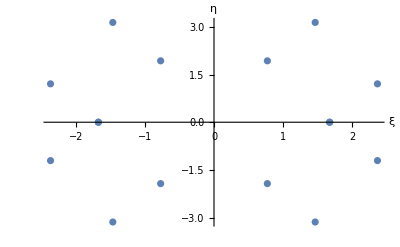

```mathematica
sub1={sp->0.99,sm->0.05,k->1,e->0.0,α->0.001};
ListPlot[{ξ,η}/.fp/.sub1,AxesLabel->{"ξ","η"},LabelStyle->15]
```

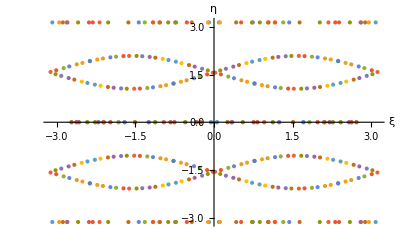

```mathematica
sub1={sp->0.99,sm->0.05,k->1,e->0};
data=Table[{ξ,η}/.fp/.sub1/.α->a1,{a1,0,2π,0.5}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15]//Quiet
```

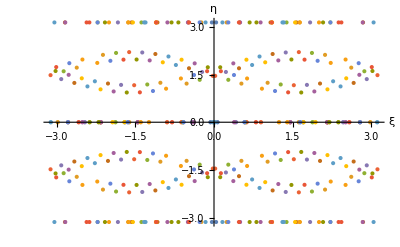

```mathematica
sub1={sp->0.99,sm->0.05,k->1,e->0.1};
data=Table[{ξ,η}/.fp/.sub1/.α->a1,{a1,0,2π,0.5}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15]//Quiet
```

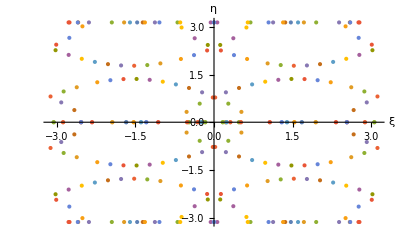

```mathematica
sub1={sp->0.99,sm->0.05,k->1,e->0.7};
data=Table[{ξ,η}/.fp/.sub1/.α->a1,{a1,0,2π,0.5}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15]//Quiet
```

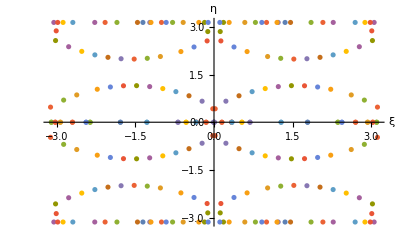

```mathematica
sub1={sp->0.99,sm->0.05,k->1,e->0.9};
data=Table[{ξ,η}/.fp/.sub1/.α->a1,{a1,0,2π,0.5}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15]//Quiet
```

Hmm.

```mathematica
fp
```

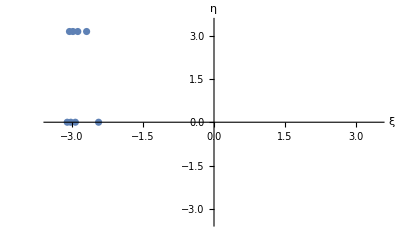

```mathematica
sub1={sp->0.99,sm->0.05,k->1,e->0.9};
data=Table[{ξ,η}/.fp[[2]]/.sub1/.α->a1,{a1,0,2π,0.5}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15,PlotRange->{{-1.1π,1.1π},{-1.1π,1.1π}}]//Quiet
```

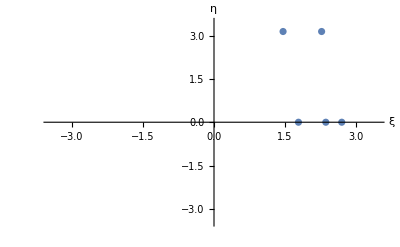

```mathematica
sub1={sp->0.99,sm->0.05,k->1,e->0.9};
data=Table[{ξ,η}/.fp[[8]]/.sub1/.α->a1,{a1,0,2π,0.5}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15,PlotRange->{{-1.1π,1.1π},{-1.1π,1.1π}}]//Quiet
```

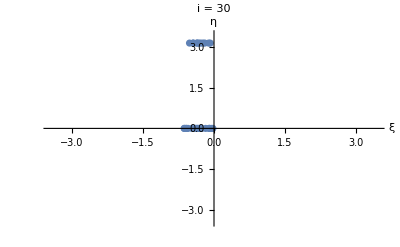
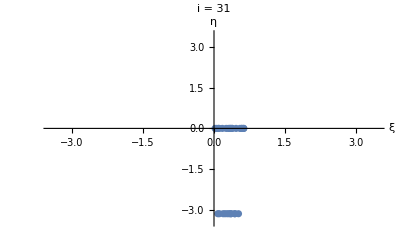
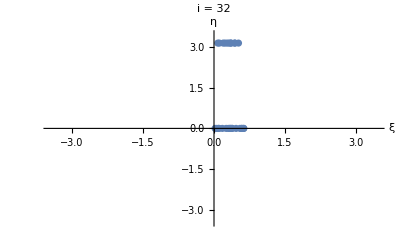
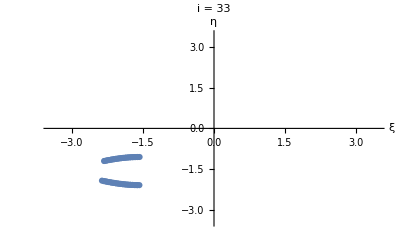
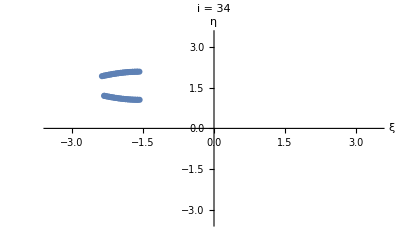
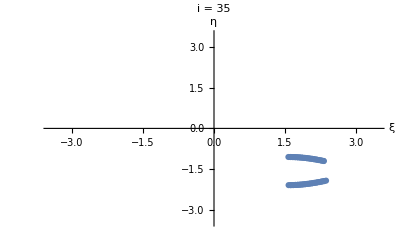
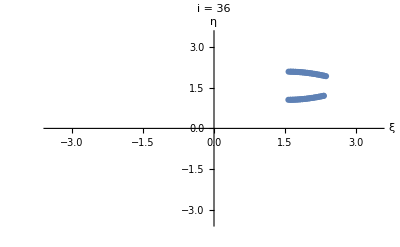
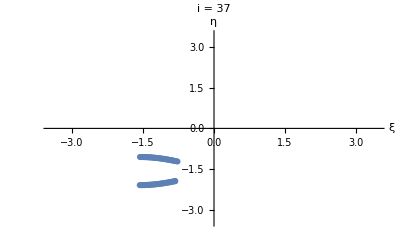

```mathematica
Table[
sub1={sp->0.99,sm->0.05,k->1,e->0.0};
data=Table[{ξ,η}/.fp[[i]]/.sub1/.α->a1,{a1,0,2π,0.1}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15,PlotRange->{{-1.1π,1.1π},{-1.1π,1.1π}},PlotLabel->"i = "<>ToString[i]]//Quiet,
{i,30,48}
]
```

## Double phase wave

$Aborted

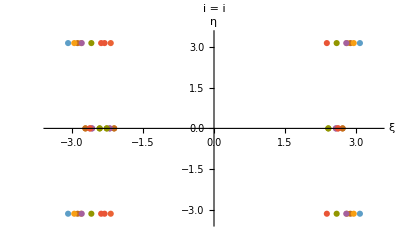

```mathematica
sub1={sp->0.99,sm->0.05,k->1,e->0.0};
data=Table[{ξ,η}/.fp[[1;;32]]/.sub1/.α->a1,{a1,0,2π,0.5}]//Quiet;
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15,PlotRange->{{-1.1π,1.1π},{-1.1π,1.1π}},PlotLabel->"i = "<>ToString[i]]//Quiet
```

```mathematica
{Cos[ξ],Cos[η]}/.fp[[1;;5]]/.e->0/.k->1//TableForm
```

Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] | (-4 sp^9 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^2+4 sp^9 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^2+128 sp^7 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^2-128 sp^7 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^2-1024 sp^5 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^2+1024 sp^5 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^2+16 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^4-768 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^4-128 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+1024 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+4096 sp^3 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+128 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4-2048 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4-4096 sp^3 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4+2048 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^4+256 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^6-1024 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^6+8192 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^6-1024 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^6-8192 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^6+1024 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^6-1024 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^8+4096 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^8-4096 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^8)/(-128 sp^6 Cos[α]^4 Sin[α]^4+512 sp^4 Cos[α]^4 Sin[α]^6)
Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] | (-4 sp^9 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^2+4 sp^9 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^2+128 sp^7 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^2-128 sp^7 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^2-1024 sp^5 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^2+1024 sp^5 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^2+16 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^4-768 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^4-128 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+1024 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+4096 sp^3 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+128 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4-2048 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4-4096 sp^3 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4+2048 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^4+256 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^6-1024 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^6+8192 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^6-1024 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^6-8192 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^6+1024 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^6-1024 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^8+4096 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^8-4096 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^8)/(-128 sp^6 Cos[α]^4 Sin[α]^4+512 sp^4 Cos[α]^4 Sin[α]^6)
Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] | (-4 sp^9 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^2+4 sp^9 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^2+128 sp^7 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^2-128 sp^7 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^2-1024 sp^5 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^2+1024 sp^5 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^2+16 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^4-768 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^4-128 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+1024 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+4096 sp^3 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+128 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4-2048 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4-4096 sp^3 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4+2048 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^4+256 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^6-1024 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^6+8192 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^6-1024 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^6-8192 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^6+1024 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^6-1024 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^8+4096 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^8-4096 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^8)/(-128 sp^6 Cos[α]^4 Sin[α]^4+512 sp^4 Cos[α]^4 Sin[α]^6)
Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] | (-4 sp^9 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^2+4 sp^9 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^2+128 sp^7 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^2-128 sp^7 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^2-1024 sp^5 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^2+1024 sp^5 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^2+16 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^4-768 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^4-128 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+1024 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+4096 sp^3 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^4+128 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4-2048 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4-4096 sp^3 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^4+2048 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^4+256 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^6-1024 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^6+8192 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^6-1024 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^6-8192 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^6+1024 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^7 Sin[α]^6-1024 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1] Sin[α]^8+4096 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^3 Sin[α]^8-4096 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,1]^5 Sin[α]^8)/(-128 sp^6 Cos[α]^4 Sin[α]^4+512 sp^4 Cos[α]^4 Sin[α]^6)
Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2] | (-4 sp^9 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2] Sin[α]^2+4 sp^9 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^3 Sin[α]^2+128 sp^7 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^3 Sin[α]^2-128 sp^7 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^5 Sin[α]^2-1024 sp^5 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^5 Sin[α]^2+1024 sp^5 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^7 Sin[α]^2+16 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2] Sin[α]^4-768 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2] Sin[α]^4-128 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^3 Sin[α]^4+1024 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^3 Sin[α]^4+4096 sp^3 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^3 Sin[α]^4+128 sp^7 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^5 Sin[α]^4-2048 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^5 Sin[α]^4-4096 sp^3 Cos[α]^7 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^5 Sin[α]^4+2048 sp^5 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^7 Sin[α]^4+256 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2] Sin[α]^6-1024 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2] Sin[α]^6+8192 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^3 Sin[α]^6-1024 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^5 Sin[α]^6-8192 sp^3 Cos[α]^5 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^5 Sin[α]^6+1024 sp^5 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^7 Sin[α]^6-1024 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2] Sin[α]^8+4096 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^3 Sin[α]^8-4096 sp^3 Cos[α]^3 Root[sp^4-8 sp^2 Sin[α]^2+16 Sin[α]^4+(-2 sp^4-32 sp^2 Cos[α]^2+40 sp^2 Sin[α]^2-128 Cos[α]^2 Sin[α]^2-128 Sin[α]^4) #1^2+(sp^4+64 sp^2 Cos[α]^2+256 Cos[α]^4-64 sp^2 Sin[α]^2+640 Cos[α]^2 Sin[α]^2+384 Sin[α]^4) #1^4+(-32 sp^2 Cos[α]^2-512 Cos[α]^4+32 sp^2 Sin[α]^2-1024 Cos[α]^2 Sin[α]^2-512 Sin[α]^4) #1^6+(256 Cos[α]^4+512 Cos[α]^2 Sin[α]^2+256 Sin[α]^4) #1^8&,2]^5 Sin[α]^8)/(-128 sp^6 Cos[α]^4 Sin[α]^4+512 sp^4 Cos[α]^4 Sin[α]^6)

```mathematica
Simplify[Cos[ξ]/.fp[[30]]/.e->0/.k->1/.sp->0]
```

Root[Sin[α]^4+(-8 Cos[α]^2 Sin[α]^2-8 Sin[α]^4) #1^2+(16 Cos[α]^4+40 Cos[α]^2 Sin[α]^2+24 Sin[α]^4) #1^4+(-32 Cos[α]^4-64 Cos[α]^2 Sin[α]^2-32 Sin[α]^4) #1^6+(16 Cos[α]^4+32 Cos[α]^2 Sin[α]^2+16 Sin[α]^4) #1^8&,8]

So its all the roots of this monster. What can be done with it? Anything? I haven’t seen the sync state, either, I guess it could be one par

```mathematica
data=Table[{ξ,η}/.fp[[2]]/.e->0/.k->1/.sp->0.01/.α->a1,{a1,0.1,2π,1}];
```

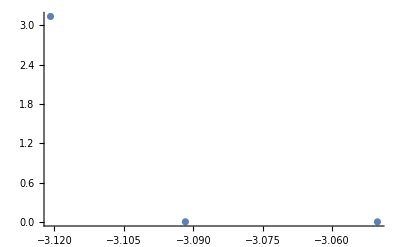

```mathematica
ListPlot[data]
```

## Flying saucers

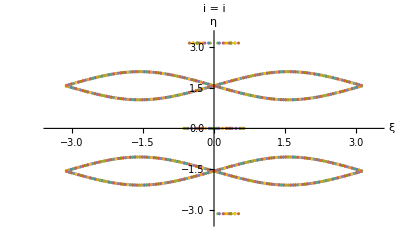

```mathematica
sub1={sp->0.99,sm->0.05,k->1,e->0.0};
data=Table[{ξ,η}/.fp[[30;;48]]/.sub1/.α->a1,{a1,0,2π,0.1}]//Quiet
ListPlot[data,AxesLabel->{"ξ","η"},LabelStyle->15,PlotRange->{{-1.1π,1.1π},{-1.1π,1.1π}},PlotLabel->"i = "<>ToString[i]]//Quiet
```

```mathematica
Simplify[{Cos[ξ],Cos[η]}/.fp[[33;;48]]]//TableForm
```

-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+k sp √(4+2 k sm Cos[α]-2 √(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+k sp √(4+2 k sm Cos[α]-2 √(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+k sp √(4+2 k sm Cos[α]-2 √(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+k sp √(4+2 k sm Cos[α]-2 √(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+k sp √(4+2 k sm Cos[α]-2 √(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+k sp √(4+2 k sm Cos[α]-2 √(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+k sp √(4+2 k sm Cos[α]-2 √(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+k sp √(4+2 k sm Cos[α]-2 √(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | -(8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+√2 k sp √(2+k sm Cos[α]+√((4-k^2 sm^2) Sin[α]^2)) (-4+k^2 sm^2+2 √((4-k^2 sm^2) Sin[α]^2)))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | -(8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+√2 k sp √(2+k sm Cos[α]+√((4-k^2 sm^2) Sin[α]^2)) (-4+k^2 sm^2+2 √((4-k^2 sm^2) Sin[α]^2)))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | -(8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+√2 k sp √(2+k sm Cos[α]+√((4-k^2 sm^2) Sin[α]^2)) (-4+k^2 sm^2+2 √((4-k^2 sm^2) Sin[α]^2)))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | -(8 e √((-4+k^2 sm^2) (-1+Cos[2 α])) Cot[α]+4 e k sm √((-4+k^2 sm^2) (-1+Cos[2 α])) Csc[α]+√2 k sp √(2+k sm Cos[α]+√((4-k^2 sm^2) Sin[α]^2)) (-4+k^2 sm^2+2 √((4-k^2 sm^2) Sin[α]^2)))/(2 √2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | (-8 e Cot[α] √((4-k^2 sm^2) Sin[α]^2)-4 e k sm Csc[α] √((4-k^2 sm^2) Sin[α]^2)+k sp √(2+k sm Cos[α]+√((4-k^2 sm^2) Sin[α]^2)) (-4+k^2 sm^2+2 √((4-k^2 sm^2) Sin[α]^2)))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | (-8 e Cot[α] √((4-k^2 sm^2) Sin[α]^2)-4 e k sm Csc[α] √((4-k^2 sm^2) Sin[α]^2)+k sp √(2+k sm Cos[α]+√((4-k^2 sm^2) Sin[α]^2)) (-4+k^2 sm^2+2 √((4-k^2 sm^2) Sin[α]^2)))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | (-8 e Cot[α] √((4-k^2 sm^2) Sin[α]^2)-4 e k sm Csc[α] √((4-k^2 sm^2) Sin[α]^2)+k sp √(2+k sm Cos[α]+√((4-k^2 sm^2) Sin[α]^2)) (-4+k^2 sm^2+2 √((4-k^2 sm^2) Sin[α]^2)))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | (-8 e Cot[α] √((4-k^2 sm^2) Sin[α]^2)-4 e k sm Csc[α] √((4-k^2 sm^2) Sin[α]^2)+k sp √(2+k sm Cos[α]+√((4-k^2 sm^2) Sin[α]^2)) (-4+k^2 sm^2+2 √((4-k^2 sm^2) Sin[α]^2)))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))

```mathematica
Simplify[{Cos[ξ],Cos[η]}/.fp[[33;;48]]/.e->0]//TableForm
```

-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (4-k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))) (k^2 sm^2-2 (2+√(-((-4+k^2 sm^2) Sin[α]^2)))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | -(k sp √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) (-4+k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | -(k sp √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) (-4+k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | -(k sp √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) (-4+k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
-1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | -(k sp √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) (-4+k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) (-4+k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) (-4+k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) (-4+k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))
1/2 √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) | (k sp √(2+k sm Cos[α]+√(-((-4+k^2 sm^2) Sin[α]^2))) (-4+k^2 sm^2+2 √(-((-4+k^2 sm^2) Sin[α]^2))))/(2 (-4+k^2 sm^2) (k sm+2 Cos[α]))

```mathematica
Integrate[1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))),{α,0,2π}]
```

∫_0^(2 π) 1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2)))ⅆα

```mathematica
Integrate[Series[1/2 √(2+k sm Cos[α]-√(-((-4+k^2 sm^2) Sin[α]^2))),{k,0,1}],{α,0,2π}]
```

(-4+k sm)/(√2)

```mathematica
Solve[(-4+k sm)/(√2)==sp,sm]
```

{{sm→(√2 (2 √2+sp))/k}}

```mathematica
Simplify[Cos[η]/.fp[[48]]/.e->0/.sm->(√2 (2 √2+sp))/k]
```

(k sp (6+4 √2 sp+sp^2+√2 √(-((6+4 √2 sp+sp^2) Sin[α]^2))) √(2+(4+√2 sp) Cos[α]+√2 √(-((6+4 √2 sp+sp^2) Sin[α]^2))))/(2 (6+4 √2 sp+sp^2) (4+√2 sp+2 Cos[α]))

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real}, {Ex,_Real}, {Eθ, _Real}, {pin, _Real, 2}, {b1,_Real},{b2,_Real}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
vel[[1,i]] = Ex + b1*Sin[pin[[1,i]] - z[[1,i]]];
vel[[2,i]] = Eθ + b2*Sin[pin[[2,i]] - z[[2,i]]];
];
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji]*Cos[thetaji]/N[n];
thetatemp=k*Sin[thetaji]*Cos[xji]/N[n];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
];
vel
(*vel/N[n]*)
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];

(*Scatter plot in (ξ,θ) space*)
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];


eulerStep[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,Ex_,Eθ_,pin_,b1_,b2_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,Ex,Eθ,pin,b1,b2];
k2=F[z+dt/2 k1,n,J,k,Ex,Eθ,pin,b1,b2];
k3=F[z+dt/2 k2,n,J,k,Ex,Eθ,pin,b1,b2];
k4=F[z+dt k3,n,J,k,Ex,Eθ,pin,b1,b2];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];

plotResults[z_,pin_]:=Block[{colors,Wp,Wm,p1,p2,p3,p4,p5,x,θ,xin,θin,x1,θ1,x2,θ2,ξ1,ξ2,η1,η2,index,n},
{x,θ}={z[[1,All]],z[[2,All]]};
{xin,θin}={pin[[1,All]],pin[[2,All]]};
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[θ,2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];

p1=Graphics[{
(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],

Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],

Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];


(*Scatter plot in (x,theta) space*)
n=Length[x];
index=Round[n/2];
{x1,θ1}={x[[1]],θ[[1]]};
{x2,θ2}={x[[index]],θ[[index]]};
p2=ListPlot[{x//mod,θ//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},Epilog->{Cyan,PointSize[0.025],Point[{x1,θ1}//mod],Magenta,Point[{x2,θ2}//mod]}];

(*Scatter plot in (ξ,θ) space*)
{ξ1,η1}={x[[1]]+θ[[1]],x[[1]]-θ[[1]]};
{ξ2,η2}={x[[index]]+θ[[index]],x[[index]]-θ[[index]]};
p3=ListPlot[{x+θ,x-θ}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]},Epilog->{Cyan,PointSize[0.025],Point[{ξ1,η1}//mod],Magenta,Point[{ξ2,η2}//mod]}];

p4=ListPlot[{x,xin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["β",15]}];

p5=ListPlot[{θ,θin}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["θ",15],Style["α",15]}];

Return[Grid[{{p1,p2,p3,p4,p5}}]
]
];
```